{{{}}}

{{{1}}}

{1/2 (-ⅇ^t+Cos[t]+Sin[t])}

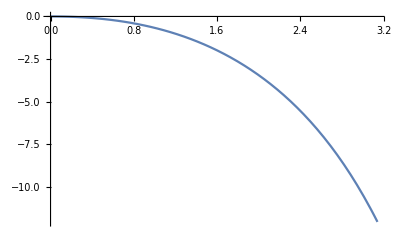

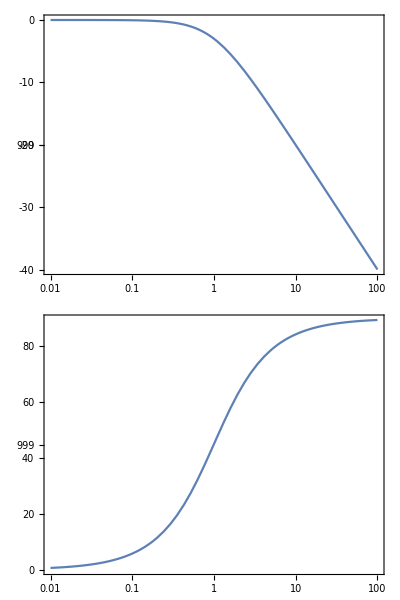

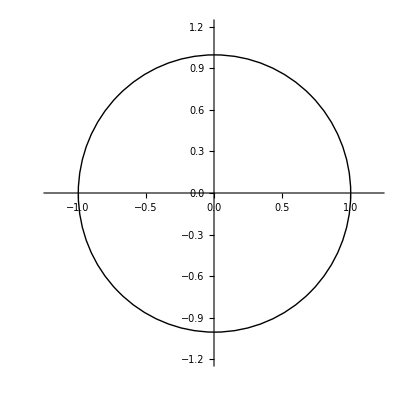

```mathematica
tf=TransferFunctionModel[1/(1-z),z];
TransferFunctionZeros[tf]
TransferFunctionPoles[tf]
OutputResponse[tf,Sin[t],t]
Plot[%,{t,0,Pi}]
BodePlot[tf,{0.01,100},ImageSize->Medium]
RootLocusPlot[ tf,{a,-1,1},PlotRange->{{-1.2,1.2},{-1.2,1.2}},Epilog->{Circle[{0,0}]}]
```

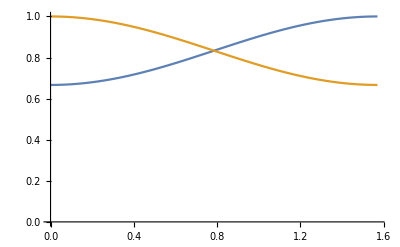

```mathematica
Plot[{2/3+Sin[t]^2/3,1-Sin[t]^2/3},{t,0,Pi/2},PlotRange->{Automatic,{0,1}}]
```